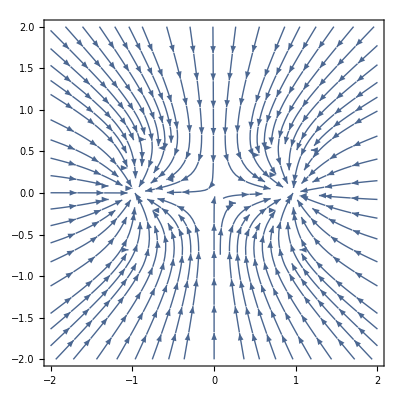

```mathematica
xdot = vx;
vxdot = -alpha*vx-x+(1-x)/(Sqrt[(1-x)^2 + (y)^2 + 0.5^2])^5 + (-1-x)/(Sqrt[(-1-x)^2 + (y)^2 + 0.5^2])^5;
ydot = vy;
vydot = -alpha*vy-y-y/(Sqrt[(1-x)^2 + (y)^2 + 0.5^2])^5 -y/(Sqrt[(-1-x)^2 + (y)^2 + 0.5^2])^5;


StreamPlot[{vxdot,vydot}/.{vx->0, vy->0, alpha -> 0.15}, {x,-2,2}, {y, -2,2}]
```

```mathematica
NSolve[{xdot == 0,vxdot == 0, ydot == 0, vydot == 0}/.alpha->0, {x,y,vx,vy}, Reals]

sol = NSolve[{xdot == 0,vxdot == 0, ydot == 0, vydot == 0}/.alpha->0.15, {x,y,vx,vy}, Reals]
```

{{x→0.967642,y→0,vx→0,vy→0},{x→-0.967642,y→0,vx→0,vy→0},{x→0,y→0,vx→0,vy→0},{x→0,y→0,vx→0,vy→0},{x→0,y→0,vx→0,vy→0},{x→0,y→0,vx→0,vy→0},{x→0,y→0,vx→0,vy→0}}

{{vy→0,vx→0,y→0,x→0.967642},{vy→0,vx→0,y→0,x→-0.967642},{vy→0,vx→0,y→0,x→0},{vy→0,vx→0,y→0,x→0},{vy→0,vx→0,y→0,x→0},{vy→0,vx→0,y→0,x→0},{vy→0,vx→0,y→0,x→0}}

```mathematica
J = {{D[xdot,x],D[xdot,y],D[xdot,vx],D[xdot,vy]},
{D[ydot,x],D[ydot,y],D[ydot,vx],D[ydot,vy]},
{D[vxdot,x],D[vxdot,y],D[vxdot,vx],D[vxdot,vy]},
{D[vydot,x],D[vydot,y],D[vydot,vx],D[vydot,vy]}}/.sol[[2]]/.alpha->0;
Eigenvalues[J]
J
```

{0.+5.71808 ⅈ,0.-5.71808 ⅈ,0.+5.64799 ⅈ,0.-5.64799 ⅈ}

{{0,0,1,0},{0,0,0,1},{-31.8998,0.,0,0},{0.,-32.6964,0,0}}

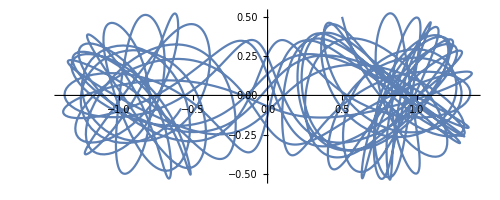

{0.576075}

{0.195286}

{0.97402}

{0.}

```mathematica
s = NDSolve[{x''[t] == -alpha*x'[t]-x[t] + (1-x[t])/(Sqrt[(1-x[t])^2 + (y[t])^2 + 0.5^2])^5 + (-1-x[t])/(Sqrt[(-1-x[t])^2 + (y[t])^2 + 0.5^2])^5, 
y''[t] == -alpha*y'[t]-y[t]-y[t]/(Sqrt[(1-x[t])^2 + (y[t])^2 + 0.5^2])^5 -y[t]/(Sqrt[(-1-x[t])^2 + (y[t])^2 + 0.5^2])^5, 
x[0] == 0.5,
y[0] == 0.5, x'[0] == y'[0] == 0
}/.alpha->0, 
{x,y},
{t,0,100}
];

ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,100},PlotRange->All]
x[2]/.s
y[2]/.s
```